```mathematica
SetDirectory[NotebookDirectory[]];
ww00= Get["cosine_bin_ww00.dat"];
ww10 = Get["cosine_bin_ww10.dat"];
```

```mathematica
ww01 = Get["cosine_bin_ww01.dat"];
```

```mathematica
ww0m1 = Get["cosine_bin_ww0m1.dat"];
wwm10 = Get["cosine_bin_wwm10.dat"];
```

```mathematica
ww11 = Get["cosine_bin_ww11.dat"];
wwm1m1 = Get["cosine_bin_wwm1m1.dat"];
ww1m1 = Get["cosine_bin_ww1m1.dat"];
wwm11 = Get["cosine_bin_wwm11.dat"];
sumww = ww00 + ww10  + ww01 + ww0m1  + wwm10  + ww11  + wwm1m1 + ww1m1  + wwm11 ;
```

```mathematica
zz00= Get["cosine_bin_zz00.dat"];
zz10 = Get["cosine_bin_zz10.dat"];
zz01 = Get["cosine_bin_zz01.dat"];
zz0m1 = Get["cosine_bin_zz0m1.dat"];
zzm10 = Get["cosine_bin_zzm10.dat"];
zz11 = Get["cosine_bin_zz11.dat"];
zzm1m1 = Get["cosine_bin_zzm1m1.dat"];
zz1m1 = Get["cosine_bin_zz1m1.dat"];
zzm11 = Get["cosine_bin_zzm11.dat"];
```

```mathematica
sumzz = zz00 + zz10  + zz01 + zz0m1  + zzm10  + zz11  + zzm1m1 + zz1m1  + zzm11 ;
```

```mathematica
pp11 = Get["cosine_bin_pp11.dat"];
ppm1m1 = Get["cosine_bin_ppm1m1.dat"];
pp1m1 = Get["cosine_bin_pp1m1.dat"];
ppm11 = Get["cosine_bin_ppm11.dat"];
```

```mathematica
sumpp =   pp11  + ppm1m1 + pp1m1  + ppm11 ;
```

```mathematica
sumpp[[400,73]]
```

-6.96063×10^-14

```mathematica
zpm10 = Get["cosine_bin_zpm10.dat"];
zp10 = Get["cosine_bin_zp10.dat"];
zp11 = Get["cosine_bin_zp11.dat"];
zpm1m1 = Get["cosine_bin_zpm1m1.dat"];
zp1m1 = Get["cosine_bin_zp1m1.dat"];
zpm11 = Get["cosine_bin_zpm11.dat"];
sumzp =  zp10+zpm10+ zp11  + zpm1m1 + zp1m1  + zpm11 ;

dytw00 =  Get["VLQ_cosine_bin_ww00.dat"];
dytww10 = Get["VLQ_cosine_bin_ww10.dat"];
dytww01 = Get["VLQ_cosine_bin_ww01.dat"];
dytww0m1 = Get["VLQ_cosine_bin_ww0m1.dat"];
dytwwm10 = Get["VLQ_cosine_bin_wwm10.dat"];
dytww1m1 = Get["VLQ_cosine_bin_ww1m1.dat"];
dytwwm11 = Get["VLQ_cosine_bin_wwm11.dat"];
dytw11 =  Get["VLQ_cosine_bin_ww11.dat"];
dytwm1m1 =  Get["VLQ_cosine_bin_wwm1m1.dat"];
```

```mathematica
dytsumww = dytw00 + dytww10  + dytww01 + dytww0m1  + dytwwm10  + dytw11  + dytwm1m1 + dytww1m1  + dytwwm11 ;
```

```mathematica
dytzz00 =  Get["VLQ_cosine_bin_zz00.dat"];
dytzz10 = Get["VLQ_cosine_bin_zz10.dat"];
dytzz01 = Get["VLQ_cosine_bin_zz01.dat"];
dytzz0m1 = Get["VLQ_cosine_bin_zz0m1.dat"];
dytzzm10 = Get["VLQ_cosine_bin_zzm10.dat"];
dytzz1m1 = Get["VLQ_cosine_bin_zz1m1.dat"];
dytzzm11 = Get["VLQ_cosine_bin_zzm11.dat"];
dytzz11 =  Get["VLQ_cosine_bin_zz11.dat"];
dytzzm1m1 =  Get["VLQ_cosine_bin_zzm1m1.dat"];
```

```mathematica
dytsumzz = dytzz00 +  dytzz10  +  dytzz01 +  dytzz0m1  +  dytzzm10  + dytzz11  + dytzzm1m1 +  dytzz1m1  +  dytzzm11 ;
```

```mathematica
dytzpm10 = Get["VLQ_cosine_bin_zpm10.dat"];
dytzp10 = Get["VLQ_cosine_bin_zp10.dat"];
dytzp11 = Get["VLQ_cosine_bin_zp11.dat"];
dytzpm1m1 = Get["VLQ_cosine_bin_zpm1m1.dat"];
dytzp1m1 = Get["VLQ_cosine_bin_zp1m1.dat"];
dytzpm11 = Get["VLQ_cosine_bin_zpm11.dat"];
dytsumzp =  dytzp10+dytzpm10+ dytzp11  + dytzpm1m1 + dytzp1m1  + dytzpm11 ;
```



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
lum = 1;
sqrtsbin = Table[350 + 25*i, {i,0,106}];
thetaList=Table[(Pi/72)*i,{i,1,71}];
factor=0.3894*10^15;
sqrtsbinnew = Table[350 + 50*i, {i,0,53}];
```

```mathematica
sumwwtable [[All, 70 ]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

```mathematica
sumwwtable = Table[{sqrtsbin[[k]],sumww[[k,j]]+sumzz[[k,j]]+sumzp[[k,j]]+ sumpp[[k,j]] },{k,1,Length@sqrtsbin},{j,2,Length@thetaList+1}];

intsumww =Table[ Interpolation[sumwwtable [[All, j ]]],{j,1,Length@thetaList} ];
```

```mathematica
integratesumww = Table[NIntegrate[lum*factor*intsumww [[j]] [ss],{ss,sqrtsbinnew[[i]],sqrtsbinnew[[i+1]]}],{i,1, 34},{j,1,Length@thetaList}];
```

```mathematica
thetawwtable = Table[{thetaList[[j]], integratesumww [[k,j]] },{k,1,34},{j,1,Length@thetaList}];
```

```mathematica
intthetaww =Table[ Interpolation[thetawwtable [[i, All]]],{i,1,34} ];
```

```mathematica
list = Table[1 - i/4,{i,0,8}]
```

{1,3/4,1/2,1/4,0,-1/4,-1/2,-3/4,-1}

```mathematica
{1,2/3,1/3,0,-1/3,-2/3,-1}
```

{1,2/3,1/3,0,-1/3,-2/3,-1}

```mathematica
cosbin = N[ArcCos[list]]
```

{0.,0.722734,1.0472,1.31812,1.5708,1.82348,2.0944,2.41886,3.14159}

```mathematica
binevents = Table[NIntegrate[Sin[θ]intthetaww [[i]][θ],{θ, cosbin[[j]],cosbin[[j+1]]}],{i,1, 34}, {j,1,Length@cosbin - 1 } ];
```

```mathematica
sumwwtable = Table[{sqrtsbin[[k]],dytsumww[[k,j]]+dytsumzz[[k,j]]+dytsumzp[[k,j]]+ sumpp[[k,j]] },{k,1,Length@sqrtsbin},{j,2,Length@thetaList+1}]

intsumww =Table[ Interpolation[sumwwtable [[All, j ]]],{j,1,Length@thetaList} ];
```

```mathematica
integratesumww = Table[NIntegrate[lum*factor*intsumww [[j]] [ss],{ss,sqrtsbinnew[[i]],sqrtsbinnew[[i+1]]}],{i,1, 34},{j,1,Length@thetaList}];
```

```mathematica
thetawwtable = Table[{thetaList[[j]], integratesumww [[k,j]] },{k,1,34},{j,1,Length@thetaList}];
```

```mathematica
intthetaww =Table[ Interpolation[thetawwtable [[i, All]]],{i,1,34} ];
```

```mathematica
list = Table[1 - i/4,{i,0,8}]
```

{1,3/4,1/2,1/4,0,-1/4,-1/2,-3/4,-1}

```mathematica
{1,2/3,1/3,0,-1/3,-2/3,-1}
```

{1,2/3,1/3,0,-1/3,-2/3,-1}

```mathematica
cosbin = N[ArcCos[list]]
```

{0.,0.722734,1.0472,1.31812,1.5708,1.82348,2.0944,2.41886,3.14159}

```mathematica
binsignal = Table[NIntegrate[Sin[θ]intthetaww [[i]][θ],{θ, cosbin[[j]],cosbin[[j+1]]}],{i,1, 34}, {j,1,Length@cosbin - 1 } ];
```

```mathematica
sqrtsbinnew [[34]]
```

2000

```mathematica
signal =binsignal - binevents;
background = binevents;
sqrtback= Sqrt[background];
chi = signal / sqrtback;
```

```mathematica
ll1 =Table[ {sqrtsbinnew [[j]],chi[[j,1]]}, {j,1,34}];
ll2 =Table[ {sqrtsbinnew [[j]],chi[[j,2]]}, {j,1,34}];
ll3 =Table[ {sqrtsbinnew [[j]],chi[[j,3]]}, {j,1,34}];
ll4 =Table[ {sqrtsbinnew [[j]],chi[[j,4]]}, {j,1,34}];
ll5 =Table[ {sqrtsbinnew [[j]],chi[[j,5]]}, {j,1,34}];
ll6 =Table[ {sqrtsbinnew [[j]],chi[[j,6]]}, {j,1,34}];
ll7 =Table[ {sqrtsbinnew [[j]],chi[[j,7]]}, {j,1,34}];
ll8 =Table[ {sqrtsbinnew [[j]],chi[[j,8]]}, {j,1,34}];
(*ll9 =Table[ {sqrtsbinnew [[j]],chi[[j,9]]}, {j,1,34}];
ll10 =Table[ {sqrtsbinnew [[j]],chi[[j,10]]}, {j,1,34}];*)
```

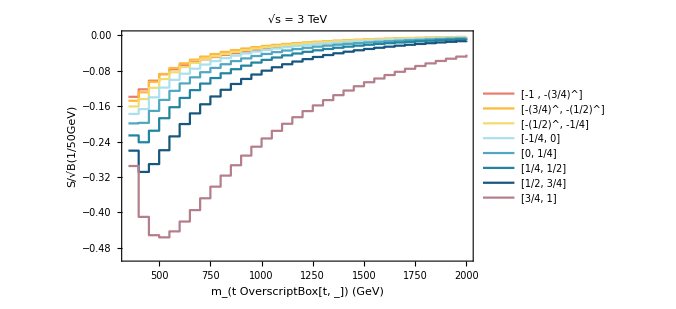

```mathematica
lineplot=ListPlot[{ll1,ll2,ll3,ll4,ll5,ll6,ll7,ll8},Joined->True,PlotStyle->{ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][2],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][5],ColorData[colorselecitonumber][6],ColorData[colorselecitonumber][7],ColorData[colorselecitonumber][8],ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][10]},Frame->True,FrameLabel->{Style[DisplayForm["m_(t OverscriptBox[t, _]) (GeV)"],Black,17,FontFamily->"Times"],Style[DisplayForm["S/√B(1/50GeV)"],Black,17,FontFamily->"Times"]},InterpolationOrder->0,
PlotLabel->Style[DisplayForm[SqrtBox["s"] ]  Row[{" = ",3 TeV}]  ,Black,17,FontFamily->"Times"],
PlotLegends->{Placed[LineLegend[{Style["[-1 , -(3/4)^]",Black,13,FontFamily->"Times"],Style["[-(3/4)^, -(1/2)^]",Black,13,FontFamily->"Times"],Style["[-(1/2)^, -1/4]",Black,13,FontFamily->"Times"],Style["[-1/4, 0]",Black,13,FontFamily->"Times"],Style["[0, 1/4]      ",Black,13,FontFamily->"Times"],Style["[1/4, 1/2]",Black,13,FontFamily->"Times"],Style["[1/2, 3/4]     ",Black,13,FontFamily->"Times"],Style["[3/4, 1]",Black,13,FontFamily->"Times"](*,Style["[2.46, π]",Black,13,FontFamily->"Times"]*)},LegendLayout->{"Row",4}],{{0.60,0.20},{0.25,0.3}}]},
(*PlotLegends->{Style["[ 0^°, 20^° ]",Black,15,FontFamily->"Times"],Style["[ 20^°, 40^°]",Black,15,FontFamily->"Times"],Style["[ 40^° , 60^°]",Black,15,FontFamily->"Times"],Style["[ 60^°, 80^°]",Black,15,FontFamily->"Times"],Style["[ 80^°, 100^°]",Black,15,FontFamily->"Times"],Style["[ 100^°, 120^°]",Black,15,FontFamily->"Times"],Style["[ 120^°, 140^°]",Black,15,FontFamily->"Times"],Style["[ 140^°, 160^°]",Black,15,FontFamily->"Times"],Style["[ 160^°, 180^°]",Black,15,FontFamily->"Times"]},*)
PlotRange->{{350,2000},{0,-0.5}},
FrameTicksStyle->Directive[Black,15],ImageSize->500]
```

```mathematica
Export["Overlay_VLQ_cosine_3TeV.pdf",lineplot]
```

Overlay_VLQ_cosine_3TeV.pdf